```mathematica
sim=Block[{i,data={},name0="Sim",name1=".csv"},For[i=1,i<=23,i++,AppendTo[data,Import["~/Work/ElektroShag/Data/Simul/"<>name0<>ToString[i]<>name1,"Table","FieldSeparators"->";"]]];data];
```

```mathematica
sim=Block[{i,data={},name0="Sim",name1=".csv"},For[i=1,i<=23,i++,AppendTo[data,Import["~/Work/ElektroShag/Data/Simul/"<>name0<>ToString[i]<>name1,"Table","FieldSeparators"->";"]]];data];
```

```mathematica
timeToVal[data_]:=DateList[data][[-1]]
```

```mathematica
Table[Length@sim[[i]],{i,Length@sim}]
```

{2501,2501,2501,2502,2502,2502,2502,2502,2502,2502,2502,2502,2502,2501,2501,2501,2501,2501,2501,2501,2501,2501,2501}

```mathematica
nodesN=Flatten[StringSplit[StringSplit[sim1[[1]][[2;;]],"_"][[All,1]],"N"],1];
```

```mathematica
tipesofdata={"f","r","u","i","P","Q","au","ai"};
```

```mathematica
datatypes=Table[Flatten[Position[Flatten[StringSplit[StringSplit[sim1[[1]][[2;;]],"_"][[All,2]],DigitCharacter]],tipesofdata[[i]]]],{i,Length@tipesofdata}];
```

```mathematica
moci=Block[{data=Transpose[sim[[1]][[2;;]][[All,datatypes[[5]]+1]]]}
```

704.528

```mathematica
StringSplit[StringSplit[sim1[[1]][[2;;]],"_"][[All,2]],LetterCharacter]
```

{{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{},{1},{2},{3},{4},{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{5},{5},{5},{6},{6},{6},{},{1},{2},{3},{4},{5},{6},{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{},{1},{2},{3},{4},{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{5},{5},{5},{},{1},{2},{3},{4},{5},{},{},{},{1},{1},{1},{},{1},{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{5},{5},{5},{6},{6},{6},{},{1},{2},{3},{4},{5},{6},{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{},{1},{2},{3},{4},{},{},{},{1},{1},{1},{2},{2},{2},{},{1},{2},{},{},{},{1},{1},{1},{},{1},{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{},{1},{2},{3},{4},{},{},{},{1},{1},{1},{2},{2},{2},{},{1},{2},{},{},{},{1},{1},{1},{2},{2},{2},{},{1},{2},{},{},{},{1},{1},{1},{},{1},{},{},{},{1},{1},{1},{},{1},{},{},{},{1},{1},{1},{},{1}}

```mathematica
Table[Mean[[[i]][[;;100]]],{i,1,Length@
```

{50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0002,50.0002,50.0002,50.0002,50.0002,50.0002,50.0002,50.0003,50.0003,50.0003,50.0003,50.0003,50.0003,50.0003,50.0004,50.0004,50.0004,50.0004,50.0004,50.0004,50.0005,50.0005,50.0005,50.0005,50.0005,50.0006,50.0006,50.0006,50.0006,50.0006,50.0007,50.0007,50.0007,50.0007,50.0007,50.0008,50.0008,50.0008,50.0008,50.0008,50.0009,50.0009,50.0009,50.0009,50.001,50.001,50.001,50.001,50.0011,50.0011,50.0011,50.0011,50.0012,50.0012,50.0012,50.0012,50.0013,50.0013,50.0013,50.0013,50.0014,50.0014,50.0014,50.0014,50.0015,50.0015,50.0015}

```mathematica
Table[Transpose[sim[[i]][[2;;]][[All,datatypes[[1]]+1]]]
```

```mathematica
Manipulate[ListPlot[Transpose[sim[[i]][[2;;]][[All,datatypes[[1]]+1]]],PlotRange->All],{i,1,Length@sim,1}]
```

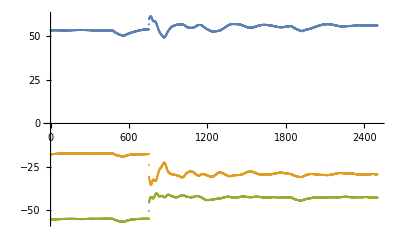

```mathematica
ListPlot[Transpose[sim[[16]][[2;;]][[All,(datatypes[[6]]+1)[[;;3]]]]],PlotRange->All]
```

```mathematica
Table[
```

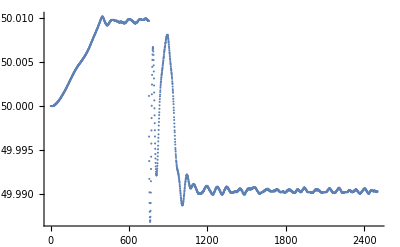

```mathematica
ListPlot[sim[[1]][[All,2]]]
```

```mathematica
sim[[1]][[1]]
```

{Time,N1_f,N1_r,N1_u,N1_i1,N1_P1,N1_Q1,N1_i2,N1_P2,N1_Q2,N1_i3,N1_P3,N1_Q3,N1_i4,N1_P4,N1_Q4,N1_au,N1_ai1,N1_ai2,N1_ai3,N1_ai4,N2_f,N2_r,N2_u,N2_i1,N2_P1,N2_Q1,N2_i2,N2_P2,N2_Q2,N2_i3,N2_P3,N2_Q3,N2_i4,N2_P4,N2_Q4,N2_i5,N2_P5,N2_Q5,N2_i6,N2_P6,N2_Q6,N2_au,N2_ai1,N2_ai2,N2_ai3,N2_ai4,N2_ai5,N2_ai6,N3_f,N3_r,N3_u,N3_i1,N3_P1,N3_Q1,N3_i2,N3_P2,N3_Q2,N3_i3,N3_P3,N3_Q3,N3_i4,N3_P4,N3_Q4,N3_au,N3_ai1,N3_ai2,N3_ai3,N3_ai4,N4_f,N4_r,N4_u,N4_i1,N4_P1,N4_Q1,N4_i2,N4_P2,N4_Q2,N4_i3,N4_P3,N4_Q3,N4_i4,N4_P4,N4_Q4,N4_i5,N4_P5,N4_Q5,N4_au,N4_ai1,N4_ai2,N4_ai3,N4_ai4,N4_ai5,N5_f,N5_r,N5_u,N5_i1,N5_P1,N5_Q1,N5_au,N5_ai1,N6_f,N6_r,N6_u,N6_i1,N6_P1,N6_Q1,N6_i2,N6_P2,N6_Q2,N6_i3,N6_P3,N6_Q3,N6_i4,N6_P4,N6_Q4,N6_i5,N6_P5,N6_Q5,N6_i6,N6_P6,N6_Q6,N6_au,N6_ai1,N6_ai2,N6_ai3,N6_ai4,N6_ai5,N6_ai6,N7_f,N7_r,N7_u,N7_i1,N7_P1,N7_Q1,N7_i2,N7_P2,N7_Q2,N7_i3,N7_P3,N7_Q3,N7_i4,N7_P4,N7_Q4,N7_au,N7_ai1,N7_ai2,N7_ai3,N7_ai4,N8_f,N8_r,N8_u,N8_i1,N8_P1,N8_Q1,N8_i2,N8_P2,N8_Q2,N8_au,N8_ai1,N8_ai2,N9_f,N9_r,N9_u,N9_i1,N9_P1,N9_Q1,N9_au,N9_ai1,N10_f,N10_r,N10_u,N10_i1,N10_P1,N10_Q1,N10_i2,N10_P2,N10_Q2,N10_i3,N10_P3,N10_Q3,N10_i4,N10_P4,N10_Q4,N10_au,N10_ai1,N10_ai2,N10_ai3,N10_ai4,N11_f,N11_r,N11_u,N11_i1,N11_P1,N11_Q1,N11_i2,N11_P2,N11_Q2,N11_au,N11_ai1,N11_ai2,N12_f,N12_r,N12_u,N12_i1,N12_P1,N12_Q1,N12_i2,N12_P2,N12_Q2,N12_au,N12_ai1,N12_ai2,N13_f,N13_r,N13_u,N13_i1,N13_P1,N13_Q1,N13_au,N13_ai1,N14_f,N14_r,N14_u,N14_i1,N14_P1,N14_Q1,N14_au,N14_ai1,N15_f,N15_r,N15_u,N15_i1,N15_P1,N15_Q1,N15_au,N15_ai1}

```mathematica
Transpose[sim[[16]][[2;;]][[All,(datatypes[[6]]+1)[[1]]]]]
```

Transpose::nmtx: The first two levels of {53.5011,53.5031,53.5081,53.512,53.5176,53.5232,53.5289,53.5347,53.5405,53.5463,53.5521,53.5578,53.5634,53.5688,53.5739,53.5788,53.5833,53.5875,53.5913,53.5947,53.5978,53.6004,53.6027,53.6046,53.6062,53.6076,53.6086,53.6094,53.61,53.6104,53.6105,53.6106,53.6104,53.6101,53.6097,53.6091,53.6084,53.6076,53.6065,53.6054,53.6041,53.6026,53.601,53.5992,53.5974,53.5954,53.5932,53.591,53.5886,53.5862,«2450»} cannot be transposed.

```mathematica
normData[data_]:=Transpose[{data[[All,1]],data[[All,2]]/data[[1,2]]}]
```

```mathematica
data=Import["~/Work/ElektroShag/crt/pointsrelations.csv","CSV","FieldSeparators"->","];data=ToExpression@Table[StringReplace[data[[i,j]],{"("->"{",")"->"}"}],{i,Length@data},{j,Length@data[[1]]}];data=Table[normData[data[[i]]],{i,Length@data}];
```

```mathematica
trdata=Table[transformddata[data[[i]]],{i,Length@data}];
```

```mathematica
trdata
```

{{{4,0.},{12,0.420311},{2,0.483768},{7,0.51785},{11,0.529695},{3,0.550249},{5,0.558586},{9,0.567964},{6,0.576783},{15,0.597485},{1,0.616564},{14,0.655651},{13,0.658939},{8,0.67425},{10,0.699628}},{{1,0.},{14,0.356184},{13,0.367019},{10,0.43583},{11,0.485493},{7,0.504688},{3,0.594997},{5,0.603367},{8,0.645369},{6,0.693392},{12,0.728996},{9,0.734927},{4,0.743666},{2,0.755924},{15,0.805982}},{{6,0.},{9,0.213509},{12,0.289569},{15,0.40514},{3,0.476711},{7,0.485437},{5,0.485766},{11,0.515015},{2,0.604506},{8,0.647134},{1,0.649637},{13,0.661813},{10,0.666647},{4,0.669777},{14,0.684985}},{{14,0.},{13,0.835261},{8,0.865779},{10,0.943971},{11,0.971464},{7,0.972568},{1,0.973266},{4,0.975015},{5,0.975834},{3,0.976479},{12,0.97757},{6,0.978285},{9,0.980179},{15,0.982871},{2,0.983365}},{{1,0.},{14,0.752347},{13,0.753492},{8,0.807215},{10,0.88719},{11,0.911144},{7,0.917255},{5,0.932523},{4,0.933985},{3,0.935507},{12,0.937834},{6,0.940884},{9,0.947621},{15,0.954905},{2,0.9592}},{{10,0.},{4,0.105196},{13,0.334813},{14,0.340738},{8,0.355593},{12,0.373318},{5,0.540326},{3,0.572931},{15,0.591764},{11,0.601311},{2,0.613277},{1,0.628072},{9,0.651572},{6,0.653623},{7,0.66353}},{{2,0.},{15,0.721974},{10,0.736462},{9,0.744983},{4,0.769797},{12,0.772179},{5,0.7965},{6,0.796506},{3,0.815166},{13,0.822231},{14,0.822576},{11,0.831788},{7,0.831846},{8,0.840018},{1,0.887447}},{{10,0.},{4,0.0650197},{12,0.219337},{13,0.387646},{8,0.388787},{14,0.396338},{11,0.622046},{5,0.714693},{2,0.734753},{3,0.748965},{1,0.786303},{7,0.803781},{15,0.881129},{6,0.904584},{9,0.912257}},{{10,0.},{15,0.30855},{13,0.409521},{14,0.416315},{8,0.425467},{4,0.426658},{9,0.430018},{12,0.549472},{5,0.739388},{3,0.796012},{1,0.811028},{6,0.814347},{11,0.856987},{7,0.865663},{2,0.868338}},{{14,1.11022×10^-16},{13,0.434557},{10,0.77426},{8,0.849305},{1,0.903463},{4,0.920954},{12,0.928185},{15,0.931621},{9,0.936119},{6,0.936623},{5,0.941777},{11,0.945799},{3,0.945987},{7,0.946458},{2,0.950664}},{{10,0.},{11,0.185615},{13,0.309879},{14,0.311427},{8,0.372229},{5,0.440512},{3,0.467512},{6,0.532428},{12,0.548237},{4,0.550651},{7,0.554369},{9,0.584874},{15,0.613725},{1,0.616196},{2,0.646086}},{{14,1.11022×10^-16},{13,0.0698086},{10,0.513787},{8,0.74302},{1,0.846338},{4,0.964744},{12,0.971584},{15,0.973173},{9,0.979726},{11,0.982014},{6,0.98257},{7,0.982804},{3,0.98686},{5,0.987458},{2,0.987681}},{{12,0.},{15,0.277896},{9,0.547036},{10,0.587394},{8,0.779877},{13,0.780278},{14,0.784205},{4,0.821672},{6,0.822071},{7,0.826264},{11,0.860867},{2,0.889901},{3,0.949026},{5,0.952616},{1,0.961607}},{{10,0.},{14,0.593797},{13,0.608465},{8,0.778239},{1,0.888945},{11,0.946983},{7,0.948834},{3,0.957724},{5,0.958448},{4,0.96422},{6,0.965454},{2,0.967597},{12,0.967675},{9,0.9682},{15,0.973724}},{{11,0.},{7,0.481022},{3,0.713999},{5,0.720702},{1,0.7521},{6,0.759036},{10,0.765105},{12,0.778224},{9,0.799932},{14,0.81184},{13,0.813505},{8,0.838611},{2,0.844337},{4,0.860018},{15,0.860146}},{{5,1.11022×10^-16},{3,0.165081},{7,0.440729},{11,0.441385},{6,0.495912},{9,0.567726},{12,0.595772},{2,0.597789},{1,0.621407},{15,0.685425},{14,0.697412},{13,0.701068},{10,0.730595},{4,0.736558},{8,0.748564}},{{15,0.},{9,0.127297},{12,0.638591},{6,0.640419},{2,0.748213},{3,0.758316},{7,0.761449},{5,0.763454},{11,0.785606},{4,0.846726},{1,0.858737},{14,0.887693},{13,0.888796},{8,0.903875},{10,0.904769}},{{10,0.},{14,0.986301},{13,0.986549},{8,0.989935},{1,0.994555},{4,0.995655},{11,0.995712},{7,0.99575},{3,0.995954},{5,0.99596},{2,0.996259},{6,0.996317},{12,0.996327},{9,0.996443},{15,0.996786}},{{11,0.},{7,0.210359},{3,0.619829},{5,0.627875},{6,0.648151},{12,0.654911},{1,0.669259},{9,0.701382},{10,0.73249},{14,0.734262},{13,0.737433},{2,0.767564},{8,0.778268},{15,0.785351},{4,0.803711}},{{1,0.},{14,0.575969},{11,0.582832},{7,0.609542},{10,0.621921},{13,0.623568},{3,0.72927},{5,0.734693},{4,0.768872},{6,0.812751},{9,0.869923},{12,0.88605},{15,0.934795},{8,0.944094},{2,0.969294}},{{11,0.},{12,0.505919},{10,0.749602},{9,0.768709},{4,0.771512},{6,0.771967},{15,0.786596},{2,0.827492},{7,0.829154},{8,0.872285},{13,0.876125},{14,0.877702},{5,0.905728},{3,0.906814},{1,0.921069}},{{4,0.},{2,0.258728},{3,0.614652},{5,0.622067},{15,0.640664},{9,0.654792},{6,0.729481},{7,0.827209},{11,0.838443},{12,0.842709},{8,0.855404},{13,0.887545},{14,0.892104},{10,0.893937},{1,0.933238}},{{12,0.},{15,0.300865},{9,0.616126},{2,0.711869},{10,0.823017},{7,0.853977},{11,0.868982},{6,0.877672},{3,0.886554},{5,0.886739},{4,0.89626},{13,0.906828},{14,0.907398},{8,0.909049},{1,0.938674}}}

```mathematica
Position[trdata,11]
```

{{1,5,1},{2,5,1},{3,8,1},{4,5,1},{5,6,1},{6,10,1},{7,12,1},{8,7,1},{9,13,1},{10,12,1},{11,2,1},{12,10,1},{13,11,1},{14,6,1},{15,1,1},{16,4,1},{17,9,1},{18,7,1},{19,1,1},{20,3,1},{21,1,1},{22,9,1},{23,7,1}}

```mathematica
num10data={11,18};num1data={2,5};num14data={4,10};num11data={15,19};
```

```mathematica
sortD[data_]:=Block[{srt1,srt2,xtic,ytic},xtic=Sort[data,#1[[1]]<#2[[1]]&][[All,1]];srt1=Sort[data[[1]],#1[[1]]<#2[[1]]&];srt2=Sort[data[[2]],#1[[1]]<#2[[1]]&];xtic=srt1[[All,1]];ytic=(srt1[[All,2]]+srt2[[All,2]])/2;Transpose[{xtic,ytic}]
]
```

```mathematica
dataAll={Sort[sortD[trdata[[num10data]]],#1[[2]]<#2[[2]]&],Sort[sortD[trdata[[num1data]]],#1[[2]]<#2[[2]]&],Sort[sortD[trdata[[num14data]]],#1[[2]]<#2[[2]]&],Sort[sortD[trdata[[num11data]]],#1[[2]]<#2[[2]]&]}[[{1,3,4}]];
```

```mathematica
transformddata[data_]:=Transpose[{data[[All,1]],(data[[All,2]]^-1-data[[1,2]]^-1)/(data[[-1,2]]^-1-data[[1,2]]^-1)}]
```

```mathematica
transformddata[data_]:=Transpose[{data[[All,1]],(data[[All,2]]^-1-1)}]
```

```mathematica
trdata=Table[transformddata[data[[i]]],{i,Length@data}];
```

```mathematica
trdata[[{1,5,7}]]
```

{{{4,0.},{12,0.311292},{2,0.402332},{7,0.461121},{11,0.483546},{3,0.525265},{5,0.543295},{9,0.564408},{6,0.585116},{15,0.637289},{1,0.690364},{14,0.817459},{13,0.829478},{8,0.888645},{10,1.}},{{1,0.},{14,0.12922},{13,0.130018},{8,0.178103},{10,0.334522},{11,0.436172},{7,0.471526},{5,0.587842},{4,0.601799},{3,0.617005},{12,0.641691},{6,0.677},{9,0.769541},{15,0.900718},{2,1.}},{{2,0.},{15,0.329346},{10,0.354423},{9,0.370503},{4,0.424112},{12,0.429872},{5,0.496406},{6,0.496423},{3,0.559342},{13,0.586614},{14,0.588002},{11,0.62715},{7,0.627411},{8,0.665935},{1,1.}}}

```mathematica
dataAll={trdata[[5]],trdata[[7]],trdata[[1]]};
```

```mathematica
dataAll
```

{{{1,0.},{14,0.752347},{13,0.753492},{8,0.807215},{10,0.88719},{11,0.911144},{7,0.917255},{5,0.932523},{4,0.933985},{3,0.935507},{12,0.937834},{6,0.940884},{9,0.947621},{15,0.954905},{2,0.9592}},{{2,0.},{15,0.721974},{10,0.736462},{9,0.744983},{4,0.769797},{12,0.772179},{5,0.7965},{6,0.796506},{3,0.815166},{13,0.822231},{14,0.822576},{11,0.831788},{7,0.831846},{8,0.840018},{1,0.887447}},{{4,0.},{12,0.420311},{2,0.483768},{7,0.51785},{11,0.529695},{3,0.550249},{5,0.558586},{9,0.567964},{6,0.576783},{15,0.597485},{1,0.616564},{14,0.655651},{13,0.658939},{8,0.67425},{10,0.699628}}}

```mathematica
pointsVal=ConstantArray[{0,0},15];
pointsVal[[1]]={0,0};
pointsVal[[2]]={dataAll[[1,-1,2]],0};
pointsVal[[4]]={x,y}/.Solve[{x^2+y^2==dataAll[[3,11,2]]^2,(x-pointsVal[[2,1]])^2+y^2==dataAll[[2,5,2]]^2},{x,y}][[2]]//Quiet
```

{0.648366,0.237117}

```mathematica
sol3=Block[{i,out={},p1=1,p2=2,p3=4},For[i=1,i≤15,i++,If[i==p1||i==p2||i==p3,Continue[]];
Block[{dis1,dis2,dis3,pos1,pos2,pos3},
pos1=Position[dataAll[[1]],i][[1,1]];
pos2=Position[dataAll[[2]],i][[1,1]];
pos3=Position[dataAll[[3]],i][[1,1]];
dis1=dataAll[[1,pos1,2]];dis2=dataAll[[2,pos2,2]];dis3=dataAll[[3,pos3,2]];AppendTo[out,{x,y}/.Solve[{x^2+y^2==dis1,(x-pointsVal[[p3,1]])^2+(y-pointsVal[[p3,2]])^2==dis3},{x,y}]]]];out]//Quiet;sol2=Block[{i,out={},p1=1,p2=2,p3=4},For[i=1,i≤15,i++,If[i==p1||i==p2||i==p3,Continue[]];
Block[{dis1,dis2,dis3,pos1,pos2,pos3},
pos1=Position[dataAll[[1]],i][[1,1]];pos2=Position[dataAll[[2]],i][[1,1]];pos3=Position[dataAll[[3]],i][[1,1]];
dis1=dataAll[[1,pos1,2]];dis2=dataAll[[2,pos2,2]];dis3=dataAll[[3,pos3,2]];AppendTo[out,{x,y}/.Solve[{x^2+y^2==dis1,(x-pointsVal[[p2,1]])^2+(y-pointsVal[[p2,2]])^2==dis2},{x,y}]]]];out]//Quiet;sol1=Block[{i,out={},p1=1,p2=2,p3=4},For[i=1,i≤15,i++,If[i==p1||i==p2||i==p3,Continue[]];
Block[{dis1,dis2,dis3,pos1,pos2,pos3},
pos1=Position[dataAll[[1]],i][[1,1]];pos2=Position[dataAll[[2]],i][[1,1]];
pos3=Position[dataAll[[3]],i][[1,1]];
dis1=dataAll[[1,pos1,2]];dis2=dataAll[[2,pos2,2]];dis3=dataAll[[3,pos3,2]];AppendTo[out,{x,y}/.Solve[{(x-pointsVal[[p2,1]])^2+(y-pointsVal[[p2,2]])^2==dis2,(x-pointsVal[[p3,1]])^2+(y-pointsVal[[p3,2]])^2==dis3},{x,y}]]]];out]//Quiet;
```

```mathematica
pointsVal[[3]]=sol1[[All,2]][[1]];
Table[pointsVal[[i+3]]=sol1[[All,2]][[i]],{i,2,12}];
pointsValR1a=pointsVal;
```

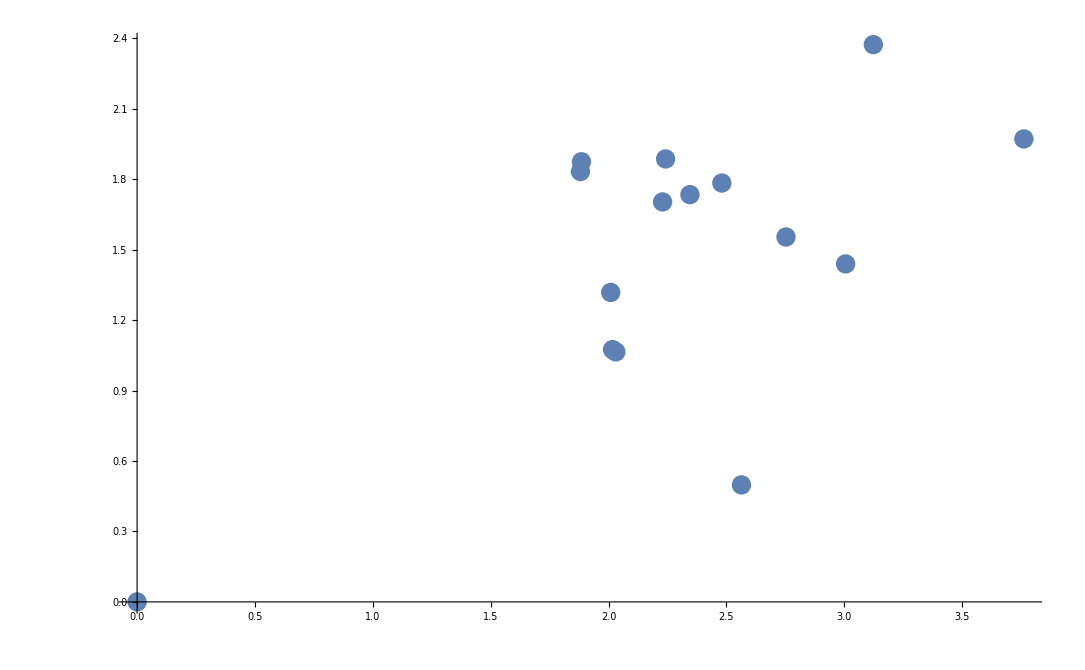

```mathematica
ListPlot[pointsValR1a+pointsValR2b+pointsValR2b]
```

```mathematica
pointsVal[[3]]=sol2[[All,2]][[1]];
Table[pointsVal[[i+3]]=sol2[[All,2]][[i]],{i,2,12}];
pointsValR2b=pointsVal;
```

```mathematica
pointsVal[[3]]=sol3[[All,2]][[1]];
Table[pointsVal[[i+3]]=sol3[[All,2]][[i]],{i,2,12}];
pointsValR3b=pointsVal;
```

```mathematica
pointsVal
```

{{-0.394909,0.838374},{-0.352574,0.334973},{0.357048,0.781903},{-0.14148-0.19169 ⅈ,-0.19169+0.14148 ⅈ},{0.519231-0.101082 ⅈ,0.703504+0.0746051 ⅈ},{-0.199587,0.868262},{0.0246096,0.562631},{-0.538965,0.782831},{-0.303477,0.814499},{0,0},{0.748735,0},{-0.333703,0.347577},{-0.486532,0.798681},{0.444626,0.602422},{-0.410464,0.791545}}

```mathematica
sol2[[All,2]]
```

{{0.917523,-0.130286},{0.424004,-0.238192},{0.641947,0.571629},{-0.14148+0.19169 ⅈ,-0.19169-0.14148 ⅈ},{0.519231+0.101082 ⅈ,0.703504-0.0746051 ⅈ},{0.888519,0.0651689},{0.530388,0.189333},{0.906903,-0.284314},{0.867762,-0.0499519},{0.430487,-0.216444},{0.906596,-0.229538},{0.877359,-0.158952}}

```mathematica
plotLabPo[pointset_]:=Table[Graphics[Text["N"<>ToString[i],{pointset[[i]][[1]],pointset[[i]][[2]]-0.05}]],{i,Length@pointset}]
```

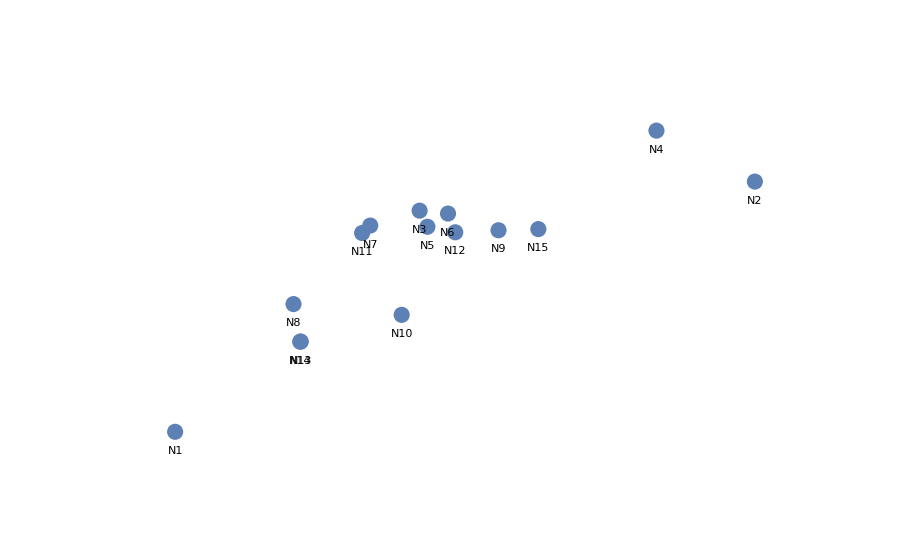

```mathematica
Show[ListPlot[{pointsValR2b},Axes->False,Frame->None,PlotRange->{{-0.2,1.4},{-0.2,1.0}}],plotLabPo[pointsValR2b]]
```

```mathematica
Export[NotebookDirectory[]<>"points.txt",pointsValR2b]
```

/home/crt/Work/ElektroShag/crt/points.txt

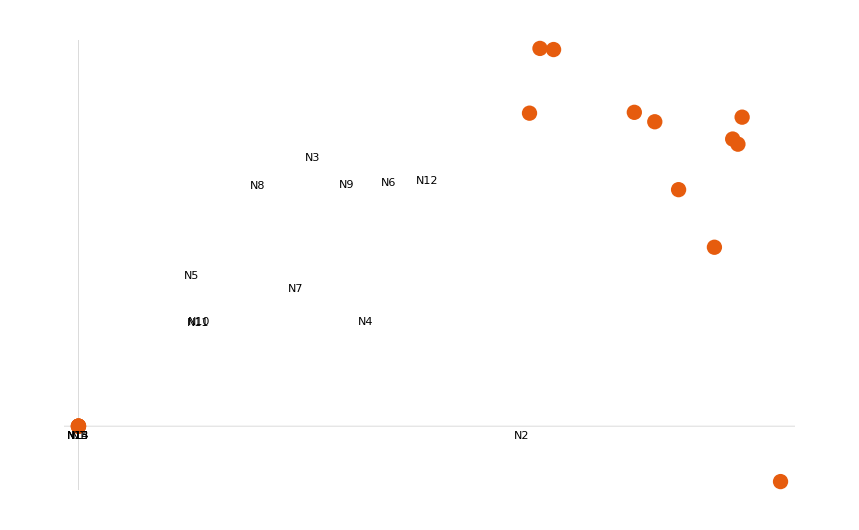

```mathematica
Show[ListPlot[{pointsValR1a},PlotTheme->"Scientific",Frame->None],plotLabPo[pointsValR1]]
```

```mathematica
pointsVali=Table[{
```

```mathematica
Table[Position[trdata[[All,;;3]],i]//Length,{i,15}]
```

{3,3,4,4,1,1,3,1,4,10,5,7,10,8,5}

```mathematica
Table[Position[trdata[[All,;;3]],i][[1]],{i,15}]
```

{{2,1,1},{1,3,1},{15,3,1},{1,1,1},{16,1,1},{3,1,1},{15,2,1},{4,3,1},{3,2,1},{6,1,1},{11,2,1},{1,2,1},{2,3,1},{2,2,1},{7,2,1}}

```mathematica
datamanage=trdata[[All,;;3]];
```

```mathematica
datamanage
```

{{{4,0.},{12,0.311292},{2,0.402332}},{{1,0.},{14,0.133177},{13,0.139577}},{{6,0.},{9,0.124845},{12,0.187448}},{{14,0.},{13,0.0857685},{8,0.109116}},{{1,0.},{14,0.12922},{13,0.130018}},{{10,0.},{4,0.059615},{13,0.255237}},{{2,0.},{15,0.329346},{10,0.354423}},{{10,0.},{4,0.0066886},{12,0.0270235}},{{10,0.},{15,0.0676608},{13,0.105159}},{{14,0.},{13,0.0398836},{10,0.177997}},{{10,0.},{11,0.124851},{13,0.245965}},{{14,0.},{13,0.000936068},{10,0.0131803}},{{12,0.},{15,0.0153652},{9,0.0482179}},{{10,0.},{14,0.0394469},{13,0.0419357}},{{11,0.},{7,0.150702},{3,0.405913}},{{5,0.},{3,0.0664128},{7,0.264697}},{{15,0.},{9,0.0153529},{12,0.185979}},{{10,0.},{14,0.232168},{13,0.236515}},{{11,0.},{7,0.0650621},{3,0.398188}},{{1,0.},{14,0.0430299},{11,0.0442588}},{{11,0.},{12,0.087748},{10,0.25654}},{{4,0.},{2,0.024969},{3,0.114107}},{{12,0.},{15,0.0281153},{9,0.104861}}}

```mathematica
Position[datamanage,2]
```

{{1,3,1},{7,1,1},{22,2,1}}

```mathematica
poival=ConstantArray[{0,0},15];
```

```mathematica
calctripcoord[data_]:=Block[{points=ConstantArray[{0,0},3]},points[[2]]={data[[2,2]],0};points[[3]]={x,y}/.Solve[{x^2+y^2==dataAll[[1,7,2]]^2,(x-pointsVal[[11,1]])^2+y^2==dataAll[[2,10,2]]^2},{x,y}][[2]]//Quiet;
```

```mathematica
pointsVal[[10]]={0,0};
pointsVal[[11]]={dataAll[[1,7,2]],0}
pointsVal[[14]]={x,y}/.Solve[{x^2+y^2==dataAll[[1,7,2]]^2,(x-pointsVal[[11,1]])^2+y^2==dataAll[[2,10,2]]^2},{x,y}][[2]]//Quiet;
```

```mathematica
trdata[[{1,5,7}]]
```

{{{4,0.},{12,0.420311},{2,0.483768},{7,0.51785},{11,0.529695},{3,0.550249},{5,0.558586},{9,0.567964},{6,0.576783},{15,0.597485},{1,0.616564},{14,0.655651},{13,0.658939},{8,0.67425},{10,0.699628}},{{1,0.},{14,0.752347},{13,0.753492},{8,0.807215},{10,0.88719},{11,0.911144},{7,0.917255},{5,0.932523},{4,0.933985},{3,0.935507},{12,0.937834},{6,0.940884},{9,0.947621},{15,0.954905},{2,0.9592}},{{2,0.},{15,0.721974},{10,0.736462},{9,0.744983},{4,0.769797},{12,0.772179},{5,0.7965},{6,0.796506},{3,0.815166},{13,0.822231},{14,0.822576},{11,0.831788},{7,0.831846},{8,0.840018},{1,0.887447}}}

```mathematica
datamanage[[All,1]]
```

{{4,0.},{1,0.},{6,0.},{14,0.},{1,0.},{10,0.},{2,0.},{10,0.},{10,0.},{14,0.},{10,0.},{14,0.},{12,0.},{10,0.},{11,0.},{5,0.},{15,0.},{10,0.},{11,0.},{1,0.},{11,0.},{4,0.},{12,0.}}

```mathematica
datamanage[[1,2,2]]
```

0.311292

```mathematica
Table[{datamanage[[i,1,1]],datamanage[[i,j,1]]},{i,Length@datamanage},{j,2,Length@datamanage[[i]]}]
```

{{{4,12},{4,2}},{{1,14},{1,13}},{{6,9},{6,12}},{{14,13},{14,8}},{{1,14},{1,13}},{{10,4},{10,13}},{{2,15},{2,10}},{{10,4},{10,12}},{{10,15},{10,13}},{{14,13},{14,10}},{{10,11},{10,13}},{{14,13},{14,10}},{{12,15},{12,9}},{{10,14},{10,13}},{{11,7},{11,3}},{{5,3},{5,7}},{{15,9},{15,12}},{{10,14},{10,13}},{{11,7},{11,3}},{{1,14},{1,11}},{{11,12},{11,10}},{{4,2},{4,3}},{{12,15},{12,9}}}

```mathematica
Print[{datamanage[[i,1,1]],datamanage[[i,j,1]],datamanage[[i,j,2]]}];
```

23

```mathematica
Block[{i,j},For[i=1,i≤Length@datamanage,i++,For[j=2,j<=Length@datamanage[[i]],j++,
AppendTo[distanceMat[[datamanage[[i,1,1]],datamanage[[i,j,1]]]],datamanage[[i,j,2]]]
]]]
```

```mathematica
datamanage=trdata[[All,;;15]];distanceMat=ConstantArray[{},{15,15}];Block[{i,j},For[i=1,i≤Length@datamanage,i++,For[j=2,j≤Length@datamanage[[i]],j++,AppendTo[distanceMat[[datamanage[[i,1,1]],datamanage[[i,j,1]]]],datamanage[[i,j,2]]];AppendTo[distanceMat[[datamanage[[i,j,1]],datamanage[[i,1,1]]]],datamanage[[i,j,2]]]]]]
```

```mathematica
distanceMat//MatrixForm
```

({} | {0.755924,0.9592,0.887447,0.969294} | {0.594997,0.935507,0.72927} | {0.616564,0.743666,0.933985,0.768872,0.933238} | {0.603367,0.932523,0.621407,0.734693} | {0.693392,0.649637,0.940884,0.812751} | {0.504688,0.917255,0.609542} | {0.645369,0.807215,0.944094} | {0.734927,0.947621,0.869923} | {0.43583,0.88719,0.628072,0.786303,0.811028,0.616196,0.888945,0.994555,0.621921} | {0.485493,0.911144,0.7521,0.669259,0.582832,0.921069} | {0.728996,0.937834,0.961607,0.88605,0.938674} | {0.367019,0.753492,0.623568} | {0.356184,0.973266,0.752347,0.903463,0.846338,0.575969} | {0.805982,0.954905,0.858737,0.934795}
{0.755924,0.9592,0.887447,0.969294} | {} | {0.815166} | {0.483768,0.769797,0.258728} | {0.7965,0.597789} | {0.604506,0.796506} | {0.831846} | {0.840018} | {0.744983} | {0.613277,0.736462,0.734753,0.868338,0.646086,0.967597,0.996259} | {0.831788,0.844337,0.767564,0.827492} | {0.772179,0.889901,0.711869} | {0.822231} | {0.983365,0.822576,0.950664,0.987681} | {0.721974,0.748213}
{0.594997,0.935507,0.72927} | {0.815166} | {} | {0.550249,0.614652} | {0.165081} | {0.476711} | {} | {} | {} | {0.572931,0.748965,0.796012,0.467512,0.957724,0.995954} | {0.713999,0.619829,0.906814} | {0.949026,0.886554} | {} | {0.976479,0.945987,0.98686} | {0.758316}
{0.616564,0.743666,0.933985,0.768872,0.933238} | {0.483768,0.769797,0.258728} | {0.550249,0.614652} | {} | {0.558586,0.736558,0.622067} | {0.576783,0.669777,0.729481} | {0.51785,0.827209} | {0.67425,0.855404} | {0.567964,0.654792} | {0.699628,0.105196,0.0650197,0.426658,0.550651,0.96422,0.995655,0.893937} | {0.529695,0.860018,0.803711,0.771512,0.838443} | {0.420311,0.821672,0.842709,0.89626} | {0.658939,0.887545} | {0.655651,0.975015,0.920954,0.964744,0.892104} | {0.597485,0.846726,0.640664}
{0.603367,0.932523,0.621407,0.734693} | {0.7965,0.597789} | {0.165081} | {0.558586,0.736558,0.622067} | {} | {0.485766,0.495912} | {0.440729} | {0.748564} | {0.567726} | {0.540326,0.714693,0.739388,0.440512,0.958448,0.730595,0.99596} | {0.720702,0.441385,0.627875,0.905728} | {0.952616,0.595772,0.886739} | {0.701068} | {0.975834,0.941777,0.987458,0.697412} | {0.685425,0.763454}
{0.693392,0.649637,0.940884,0.812751} | {0.604506,0.796506} | {0.476711} | {0.576783,0.669777,0.729481} | {0.485766,0.495912} | {} | {0.485437} | {0.647134} | {0.213509} | {0.666647,0.653623,0.904584,0.814347,0.532428,0.965454,0.996317} | {0.515015,0.759036,0.648151,0.771967} | {0.289569,0.822071,0.877672} | {0.661813} | {0.684985,0.978285,0.936623,0.98257} | {0.40514,0.640419}
{0.504688,0.917255,0.609542} | {0.831846} | {} | {0.51785,0.827209} | {0.440729} | {0.485437} | {} | {} | {} | {0.66353,0.803781,0.865663,0.554369,0.948834,0.99575} | {0.481022,0.210359,0.829154} | {0.826264,0.853977} | {} | {0.972568,0.946458,0.982804} | {0.761449}
{0.645369,0.807215,0.944094} | {0.840018} | {} | {0.67425,0.855404} | {0.748564} | {0.647134} | {} | {} | {} | {0.355593,0.388787,0.425467,0.372229,0.778239,0.989935} | {0.838611,0.778268,0.872285} | {0.779877,0.909049} | {} | {0.865779,0.849305,0.74302} | {0.903875}
{0.734927,0.947621,0.869923} | {0.744983} | {} | {0.567964,0.654792} | {0.567726} | {0.213509} | {} | {} | {} | {0.651572,0.912257,0.430018,0.584874,0.9682,0.996443} | {0.799932,0.701382,0.768709} | {0.547036,0.616126} | {} | {0.980179,0.936119,0.979726} | {0.127297}
{0.43583,0.88719,0.628072,0.786303,0.811028,0.616196,0.888945,0.994555,0.621921} | {0.613277,0.736462,0.734753,0.868338,0.646086,0.967597,0.996259} | {0.572931,0.748965,0.796012,0.467512,0.957724,0.995954} | {0.699628,0.105196,0.0650197,0.426658,0.550651,0.96422,0.995655,0.893937} | {0.540326,0.714693,0.739388,0.440512,0.958448,0.730595,0.99596} | {0.666647,0.653623,0.904584,0.814347,0.532428,0.965454,0.996317} | {0.66353,0.803781,0.865663,0.554369,0.948834,0.99575} | {0.355593,0.388787,0.425467,0.372229,0.778239,0.989935} | {0.651572,0.912257,0.430018,0.584874,0.9682,0.996443} | {} | {0.601311,0.622046,0.856987,0.185615,0.946983,0.765105,0.995712,0.73249,0.749602} | {0.373318,0.219337,0.549472,0.548237,0.587394,0.967675,0.996327,0.823017} | {0.334813,0.387646,0.409521,0.309879,0.608465,0.986549} | {0.943971,0.340738,0.396338,0.416315,0.77426,0.311427,0.513787,0.593797,0.986301} | {0.591764,0.881129,0.30855,0.613725,0.973724,0.904769,0.996786}
{0.485493,0.911144,0.7521,0.669259,0.582832,0.921069} | {0.831788,0.844337,0.767564,0.827492} | {0.713999,0.619829,0.906814} | {0.529695,0.860018,0.803711,0.771512,0.838443} | {0.720702,0.441385,0.627875,0.905728} | {0.515015,0.759036,0.648151,0.771967} | {0.481022,0.210359,0.829154} | {0.838611,0.778268,0.872285} | {0.799932,0.701382,0.768709} | {0.601311,0.622046,0.856987,0.185615,0.946983,0.765105,0.995712,0.73249,0.749602} | {} | {0.860867,0.778224,0.654911,0.505919,0.868982} | {0.813505,0.737433,0.876125} | {0.971464,0.945799,0.982014,0.81184,0.734262,0.877702} | {0.860146,0.785606,0.785351,0.786596}
{0.728996,0.937834,0.961607,0.88605,0.938674} | {0.772179,0.889901,0.711869} | {0.949026,0.886554} | {0.420311,0.821672,0.842709,0.89626} | {0.952616,0.595772,0.886739} | {0.289569,0.822071,0.877672} | {0.826264,0.853977} | {0.779877,0.909049} | {0.547036,0.616126} | {0.373318,0.219337,0.549472,0.548237,0.587394,0.967675,0.996327,0.823017} | {0.860867,0.778224,0.654911,0.505919,0.868982} | {} | {0.780278,0.906828} | {0.97757,0.928185,0.971584,0.784205,0.907398} | {0.277896,0.638591,0.300865}
{0.367019,0.753492,0.623568} | {0.822231} | {} | {0.658939,0.887545} | {0.701068} | {0.661813} | {} | {} | {} | {0.334813,0.387646,0.409521,0.309879,0.608465,0.986549} | {0.813505,0.737433,0.876125} | {0.780278,0.906828} | {} | {0.835261,0.434557,0.0698086} | {0.888796}
{0.356184,0.973266,0.752347,0.903463,0.846338,0.575969} | {0.983365,0.822576,0.950664,0.987681} | {0.976479,0.945987,0.98686} | {0.655651,0.975015,0.920954,0.964744,0.892104} | {0.975834,0.941777,0.987458,0.697412} | {0.684985,0.978285,0.936623,0.98257} | {0.972568,0.946458,0.982804} | {0.865779,0.849305,0.74302} | {0.980179,0.936119,0.979726} | {0.943971,0.340738,0.396338,0.416315,0.77426,0.311427,0.513787,0.593797,0.986301} | {0.971464,0.945799,0.982014,0.81184,0.734262,0.877702} | {0.97757,0.928185,0.971584,0.784205,0.907398} | {0.835261,0.434557,0.0698086} | {} | {0.982871,0.931621,0.973173,0.887693}
{0.805982,0.954905,0.858737,0.934795} | {0.721974,0.748213} | {0.758316} | {0.597485,0.846726,0.640664} | {0.685425,0.763454} | {0.40514,0.640419} | {0.761449} | {0.903875} | {0.127297} | {0.591764,0.881129,0.30855,0.613725,0.973724,0.904769,0.996786} | {0.860146,0.785606,0.785351,0.786596} | {0.277896,0.638591,0.300865} | {0.888796} | {0.982871,0.931621,0.973173,0.887693} | {})

```mathematica
combinations0=Block[{i,j,k,l,comb={}},For[i=1,i≤Length@distanceMat,i++,
For[j=i+1,j≤Length@distanceMat,j++,If[Length[distanceMat[[i,j]]]==0,Continue[]];
For[k=1,k≤Length@distanceMat,k++,If[Length[distanceMat[[j,k]]]==0||k==i,Continue[]];
If[Length[distanceMat[[k,i]]]==0,Continue[]];
If[];AppendTo[comb,{i,j,k}]]]];comb]
```

{{1,13,14},{1,14,13},{2,4,10},{2,10,4},{2,10,15},{2,15,10},{4,10,2},{4,10,12},{4,12,10},{6,9,12},{6,12,9},{9,12,6},{9,12,15},{9,15,12},{10,11,12},{10,12,4},{10,12,11},{10,12,15},{10,13,14},{10,14,13},{10,15,2},{10,15,12},{11,12,10},{12,15,9},{12,15,10},{13,14,1},{13,14,10}}

```mathematica
calculatePos[comb_]:=Block[{data={Mean@distanceMat[[comb[[1]],comb[[2]]]],Mean@distanceMat[[comb[[1]],comb[[3]]]],Mean@distanceMat[[comb[[2]],comb[[3]]]]},points=ConstantArray[{0,0},3]},
points[[2]]={data[[1]],0};
points[[3]]={x,y}/.Solve[{x^2+y^2==data[[2]]^2,(x-points[[2,1]])^2+y^2==data[[3]]^2},{x,y}][[2]]//Quiet;points]
```

```mathematica
Table[calculatePos[combinations[[i]]],{i,Length@combinations}]
```

{{{0,0},{0.609542,0},{0.485391,0.322627}},{{0,0},{0.807215,0},{0.037124,0.434246}},{{0,0},{0.807215,0},{0.183046,0.530826}},{{0,0},{0.43583,0},{0.0687587,0.804282}},{{0,0},{0.43583,0},{0.356771,0.460877}},{{0,0},{0.43583,0},{0.284114,0.482872}},{{0,0},{0.43583,0},{0.152627,0.540358}},{{0,0},{0.582832,0},{0.507636,0.337413}},{{0,0},{0.582832,0},{0.266786,0.344634}},{{0,0},{0.560256,0},{0.221016,0.375632}},{{0,0},{0.560256,0},{0.383547,0.41009}},{{0,0},{0.5615,0},{0.263148,0.763119}},{{0,0},{0.5615,0},{0.118467,0.41942}},{{0,0},{0.5615,0},{0.382697,0.409182}},{{0,0},{0.371248,0},{0.906346,0.+0.528286 ⅈ}},{{0,0},{0.371248,0},{0.6302,0.331067}},{{0,0},{0.744983,0},{0.485596,0.520533}},{{0,0},{0.744983,0},{0.711454,0.122802}},{{0,0},{0.736462,0},{0.456886,0.+0.266307 ⅈ}},{{0,0},{0.736462,0},{0.601817,0.380229}},{{0,0},{0.736462,0},{0.657481,0.298271}},{{0,0},{0.711869,0},{0.328657,0.172655}},{{0,0},{0.711869,0},{0.508184,0.544747}},{{0,0},{0.711869,0},{0.622608,0.393365}},{{0,0},{0.711869,0},{0.606392,0.391836}},{{0,0},{0.721974,0},{0.734127,0.126715}},{{0,0},{0.721974,0},{0.670675,0.304256}},{{0,0},{0.721974,0},{0.597905,0.386352}},{{0,0},{0.614652,0},{0.0147087,0.164424}},{{0,0},{0.165081,0},{0.0547654,0.612208}},{{0,0},{0.165081,0},{0.351434,0.566806}},{{0,0},{0.666914,0},{0.0869903,0.140301}},{{0,0},{0.622067,0},{0.592792,0.162464}},{{0,0},{0.622067,0},{0.370454,0.361847}},{{0,0},{0.51785,0},{0.445007,0.434668}},{{0,0},{0.0851077,0},{-2.33415,0.+2.30443 ⅈ}},{{0,0},{0.0851077,0},{0.124554,0.401432}},{{0,0},{0.420311,0},{-0.228725,0.292421}},{{0,0},{0.420311,0},{0.0252207,0.0812849}},{{0,0},{0.440729,0},{0.35514,0.510728}},{{0,0},{0.440729,0},{0.488663,0.342351}},{{0,0},{0.596654,0},{-0.0515598,0.156822}},{{0,0},{0.596654,0},{0.36096,0.252884}},{{0,0},{0.213509,0},{-0.488975,0.+0.394013 ⅈ}},{{0,0},{0.213509,0},{0.708823,0.+0.478677 ⅈ}},{{0,0},{0.289569,0},{-0.360537,0.+0.290518 ⅈ}},{{0,0},{0.289569,0},{0.332369,0.403521}},{{0,0},{0.522779,0},{0.289491,0.+0.195497 ⅈ}},{{0,0},{0.522779,0},{0.1841,0.223511}},{{0,0},{0.345691,0},{0.21891,0.568876}},{{0,0},{0.345691,0},{-0.0611121,0.436472}},{{0,0},{0.884087,0},{0.703132,0.396488}},{{0,0},{0.884087,0},{0.611242,0.545662}},{{0,0},{0.819368,0},{0.614912,0.522953}},{{0,0},{0.819368,0},{0.659522,0.588762}},{{0,0},{0.768709,0},{0.437875,0.382757}},{{0,0},{0.581581,0},{0.332265,0.666783}},{{0,0},{0.581581,0},{0.257894,0.+0.144649 ⅈ}},{{0,0},{0.581581,0},{0.578764,0.505911}},{{0,0},{0.581581,0},{0.163159,0.+0.102061 ⅈ}},{{0,0},{0.127297,0},{0.196223,0.718677}},{{0,0},{0.127297,0},{-0.830766,0.+0.802862 ⅈ}},{{0,0},{0.127297,0},{0.745425,0.+0.466284 ⅈ}},{{0,0},{0.467609,0},{0.0736861,0.429555}},{{0,0},{0.467609,0},{0.134095,0.380424}},{{0,0},{0.403366,0},{0.245834,0.69422}},{{0,0},{0.403366,0},{-0.008323,0.0846998}},{{0,0},{0.403366,0},{0.155452,0.441013}},{{0,0},{0.403366,0},{0.115585,0.286083}},{{0,0},{0.506146,0},{0.130639,0.41579}},{{0,0},{0.506146,0},{0.423766,0.438878}},{{0,0},{0.610074,0},{0.202316,0.386025}},{{0,0},{0.610074,0},{0.395392,0.790743}},{{0,0},{0.610074,0},{0.351575,0.364113}},{{0,0},{0.30855,0},{0.188515,0.711926}},{{0,0},{0.30855,0},{0.151104,0.373994}},{{0,0},{0.505919,0},{0.50268,0.581572}},{{0,0},{0.505919,0},{0.308259,0.351617}},{{0,0},{0.405784,0},{0.185039,0.6874}},{{0,0},{0.405784,0},{-0.0305424,0.287954}},{{0,0},{0.405784,0},{0.599694,0.+0.146276 ⅈ}},{{0,0},{0.405784,0},{0.286065,0.284378}},{{0,0},{0.446542,0},{0.221708,0.514521}},{{0,0},{0.446542,0},{0.093376,0.497458}}}

```mathematica
Block[{comb=combinations[[1]]},{distanceMat[[comb[[1]],comb[[2]]]],distanceMat[[comb[[1]],comb[[3]]]],distanceMat[[comb[[2]],comb[[3]]]]}]
```

{{0.367019,0.753492},{0.356184,0.752347,0.575969},{0.835261,0.434557,0.0698086}}

```mathematica
Block[{comb=combinations[[1]]},{Mean@distanceMat[[comb[[1]],comb[[2]]]],Mean@distanceMat[[comb[[1]],comb[[3]]]],Mean@distanceMat[[comb[[2]],comb[[3]]]]}]
```

{0.560256,0.5615,0.446542}

```mathematica
{x,y}/.Solve[{x^2+y^2==dataAll[[1,7,2]]^2,(x-pointsVal[[11,1]])^2+y^2==dataAll[[2,10,2]]^2},{x,y}][[2]]//Quiet;
```